/Users/mario.fernandeznavarro/Library/CloudStorage/GoogleDrive-mariofnavarro.physics@gmail.com/My Drive/Physics/Projects/LeptonAsymmetries/COFLASY-C_github/github_v1/COFLASY-COFLASY-C/output

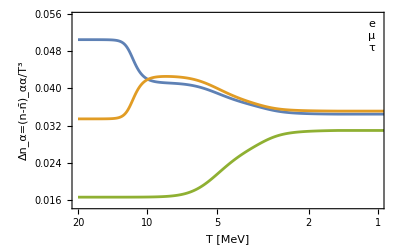

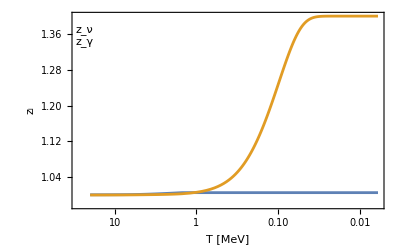

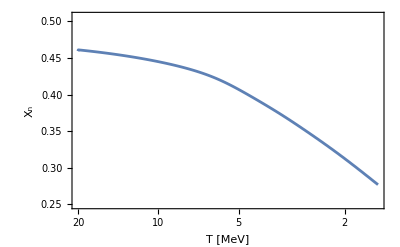

```mathematica
dir=SetDirectory[NotebookDirectory[]];
Print[dir]

(* load data *)
dataPlot=Import[FileNameJoin[{dir,"asym_evolve_results.dat"}],HeaderLines->1];
dataXnPlot=Import[FileNameJoin[{dir, "Xn_evolve_results.dat"}],HeaderLines->1]/.{a1_,a2_}->{20/a1,a2};


(* plot asymmetry and Subscript[z, i] evolution *)
ListLogLinearPlot[{dataPlot[[All,{1,4}]],dataPlot[[All,{1,3}]],dataPlot[[All,{1,2}]]},Joined->True,ScalingFunctions->{"Reverse","Linear"},Frame->True,FrameLabel->{"T [MeV]","Δn_α=(n-n̄)_αα/T^3"},PlotRange->{{20,1},{1.1 Max[dataPlot[[All,2]],dataPlot[[All,3]],dataPlot[[All,4]]],If[Min[dataPlot[[All,2]],dataPlot[[All,3]],dataPlot[[All,4]]]<=0,1.1 Min[dataPlot[[All,2]],dataPlot[[All,3]],dataPlot[[All,4]]],0.9 Min[dataPlot[[All,2]],dataPlot[[All,3]],dataPlot[[All,4]]]]}},Epilog->{Inset[Framed[Column[{Style["e",ColorData[97][1],11],Style["μ",ColorData[97][2],11],Style["τ",ColorData[97][3],11]}]],Scaled[{0.96,0.88}]]}]

ListLogLinearPlot[{dataPlot[[All,{1,5}]],dataPlot[[All,{1,6}]]},Joined->True,PlotRange->All,Frame->True,ScalingFunctions->{"Reverse",None},FrameLabel->{"T [MeV]","z_i"},Epilog->{Inset[Framed[Column[{Style["z_ν",ColorData[97][1],11],Style["z_γ",ColorData[97][2],11]}]],Scaled[{0.04,0.88}]]}]



(* plot Subscript[X, n] evolution *)
ListLogLinearPlot[dataXnPlot,Joined->True,ScalingFunctions->{"Reverse","Linear"},Frame->True,FrameLabel->{"T [MeV]","X_n"},PlotRange->{{20,Min[dataXnPlot[[All,1]]]},{1.1 Max[dataXnPlot[[All,2]]],0.9 Min[dataXnPlot[[All,2]]]}}]
```